```mathematica
Clear[pm,partialTrace, single, czGate, channel];
pm[i_]:= PauliMatrix[i];

partialTrace[matrix_,lengths_,indicesToKeep_]:=
(*matrix: input state. lengths are the dimensions e.g. 3 qubits {2,2,2,2}. indicesToKeep: qubits to keep.*)
With[{indicesToTrace=Complement[Range@Length@lengths,indicesToKeep]},With[{matrixInTPForm=Transpose[ArrayReshape[matrix,Join[lengths,lengths]],Join@@Transpose@Partition[Range[2 Length@lengths],2]]},Flatten[TensorContract[matrixInTPForm,{2 #-1,2 #}&/@indicesToTrace],Transpose@Partition[Range[2 Length@lengths-2 Length@indicesToTrace],2]]]];

single[n_,switch_,matrix_]:= (*n: number of qubits. switch: qubit to apply matrix to*)KroneckerProduct@@ReplacePart[ConstantArray[IdentityMatrix[2],n],switch->matrix];

cxGate[n_,control_,target_]:=Divide[1,2](IdentityMatrix[2^n]+single[n, control, pm[3]]+single[n,target,pm[1]]-single[n, control, pm[3]].single[n,target,pm[1]]);
czGate[n_,control_,target_]:= Divide[1,2](IdentityMatrix[2^n]+single[n, control, pm[3]]+single[n,target,pm[3]]-single[n, control, pm[3]].single[n,target,pm[3]]);

channel[n_,switch_,p_,state_]:= 
(*Depolarizing channel. n: number of qubits. switch: qubit sent into the channel. p is the probability. state: is the input.*)
(1-Divide[3p,4])state+Divide[p,4]Sum[single[n,switch,PauliMatrix[i]].state.single[n,switch,PauliMatrix[i]],{i,1,3}];

zMeas[0] = {{1,0},{0,0}};
zMeas[1] = {{0,0},{0,1}};
```

```mathematica
partialTrace[UnitVector[2^8,1],{2,2,2,2,2,2,2,2},{8}]
```

{{1,0},{0,0}}

```mathematica
ket0={{1},{0}};
ket1={{0},{1}};
bra0=Transpose[ket0];
bra1=Transpose[ket1];
ketPlus=1/Sqrt[2](ket0+ket1);
ketPhiPlus=1/Sqrt[2](KroneckerProduct[ket0,ket0]+KroneckerProduct[ket1, ket1]);
rhoPhiPlus=ketPhiPlus.Transpose[ketPhiPlus];
rhoPlus=ketPlus.Transpose[ketPlus];
```

```mathematica
nqubits=6;
rho0=KroneckerProduct[rhoPlus, rhoPlus, rhoPlus, rhoPlus, rhoPhiPlus]; (*State before left checks*)
pcsLeftU=cxGate[nqubits,1,5].czGate[nqubits,2,5].cxGate[nqubits,4,6].czGate[nqubits,3,6] ;
pcsRightU=Transpose[pcsLeftU];
rho1=pcsLeftU.rho0.Transpose[pcsLeftU]; (*left PCS checks*)
rho2=rho1;
rho2=FullSimplify[channel[nqubits,1,p2,  rho2]];
rho2=FullSimplify[channel[nqubits,2,p2,  rho2]];
rho2=FullSimplify[channel[nqubits,3,p1,  rho2]];
rho2=FullSimplify[channel[nqubits,4,p1,  rho2]];
rho2=FullSimplify[channel[nqubits,5,p2,  rho2]];
rho2=FullSimplify[channel[nqubits,6,p1,  rho2]]; (*State after noise*)
rho3=pcsRightU.rho2.Transpose[pcsRightU]; (*right PCS checks.*)
(*Post measurement state unormalized*)
rho4=FullSimplify[single[nqubits, 1, rhoPlus].single[nqubits, 2, rhoPlus].single[nqubits, 3, rhoPlus].single[nqubits, 4, rhoPlus].rho3.single[nqubits, 1, rhoPlus].single[nqubits, 2, rhoPlus].single[nqubits, 3, rhoPlus].single[nqubits, 4, rhoPlus]];
finalNormalizedSt=FullSimplify[rho4/Tr[rho4]];
noisyBellSt=partialTrace[finalNormalizedSt,{2,2,2,2,2,2}, {5,6}] (*Final normalized state*)
```

{{(8+6 (-2+p2) p2-3 p1 (4+3 (-2+p2) p2)+p1^2 (6+p2 (-9+5 p2)))/(4 (2+p1 (-3+2 p1)) (2+p2 (-3+2 p2))),0,0,(2 (-1+p1)^2 (-1+p2)^2)/((2+p1 (-3+2 p1)) (2+p2 (-3+2 p2)))},{0,(2 p2^2-3 p1 p2^2+p1^2 (2+3 (-1+p2) p2))/(4 (2+p1 (-3+2 p1)) (2+p2 (-3+2 p2))),0,0},{0,0,(2 p2^2-3 p1 p2^2+p1^2 (2+3 (-1+p2) p2))/(4 (2+p1 (-3+2 p1)) (2+p2 (-3+2 p2))),0},{(2 (-1+p1)^2 (-1+p2)^2)/((2+p1 (-3+2 p1)) (2+p2 (-3+2 p2))),0,0,(8+6 (-2+p2) p2-3 p1 (4+3 (-2+p2) p2)+p1^2 (6+p2 (-9+5 p2)))/(4 (2+p1 (-3+2 p1)) (2+p2 (-3+2 p2)))}}

```mathematica
FullSimplify[Tr[noisyBellSt]]
```

1

```mathematica
postr=FullSimplify[Tr[rho4]] (*post selection rate*)
fidelity=FullSimplify[Tr[noisyBellSt.rhoPhiPlus]] (*Fidelity*)
```

1/16 (-2+p1) (2+p1 (-3+2 p1)) (-2+p2) (2+p2 (-3+2 p2))

(16+14 (-2+p1) p1-28 p2-25 (-2+p1) p1 p2+(14+p1 (-25+13 p1)) p2^2)/(4 (2+p1 (-3+2 p1)) (2+p2 (-3+2 p2)))

```mathematica
postr//TeXForm
```

\frac{1}{16} (\text{p1}-2) (\text{p1} (2 \text{p1}-3)+2) (\text{p2}-2) (\text{p2} (2 \text{p2}-3)+2)

```mathematica
fidelity//TeXForm
```

\frac{(\text{p1} (13 \text{p1}-25)+14) \text{p2}^2-25 (\text{p1}-2) \text{p1} \text{p2}+14 (\text{p1}-2) \text{p1}-28 \text{p2}+16}{4 (\text{p1} (2 \text{p1}-3)+2) (\text{p2} (2
   \text{p2}-3)+2)}

```mathematica
(*Let p1=p2*)
postrEqual=FullSimplify[postr/.{p1->p,p2->p}]
fidelityEqual=FullSimplify[fidelity/.{p1->p,p2->p}]
```

1/16 (-2+p)^2 (2+p (-3+2 p))^2

(16+p (-56+p (78+p (-50+13 p))))/(4 (2+p (-3+2 p))^2)

```mathematica
Series[((4-9 p+6 p^2) (4+p (-5+2 p)))/(4 (2+p (-3+2 p))^2),{p,0,2}]
```

1-p/2-(15 p^2)/16+O[p]^3

```mathematica
(*Get the initial fidelity of the noisy Bell state without PCS*)
initialF=FullSimplify[Tr[channel[2,2,p,channel[2,1,p,rhoPhiPlus]].rhoPhiPlus]]
Solve[F==initialF,p]
```

1+3/4 (-2+p) p

{{p→1/3 (3-√3 √(-1+4 F))},{p→1/3 (3+√3 √(-1+4 F))}}

```mathematica
(*In terms of initial F*)
postrInitialF=FullSimplify[postrEqual/.p->1/3 (3-√3 √(-1+4 F))]
fidelityInitialF=FullSimplify[fidelityEqual/.p->1/3 (3-√3 √(-1+4 F))]
```

1/324 (3+6 F-√(-3+12 F)+4 F √(-3+12 F))^2

(1+52 F^2-√(-3+12 F)-2 F (4+√(-3+12 F)))/(-1-8 F+√(-3+12 F))^2

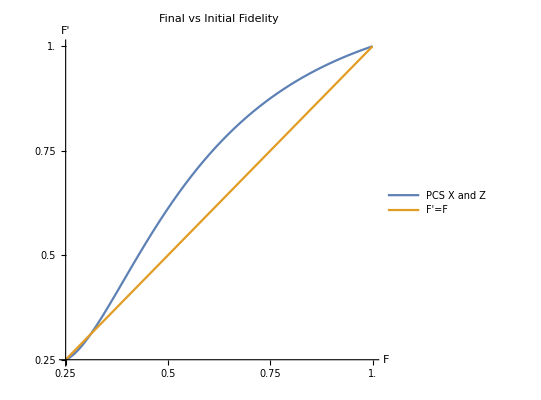

```mathematica
plot1=Plot[{fidelityInitialF, F},{F,1/4,1}, PlotLegends->Placed[{"PCS X and Z", "F'=F"},{Right, Center}], AxesLabel->{"F", "F'"}, AspectRatio->1, PlotLabel->"Final vs Initial Fidelity", Ticks->{Range[1/4,1,0.25],Range[1/4,1,0.25]}]
```

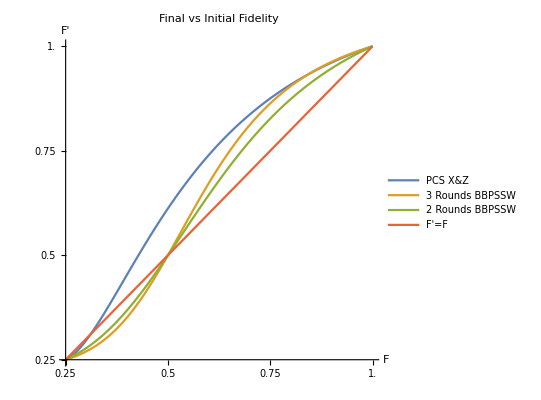

```mathematica
fidpcs[F_]:=(1+52 F^2-√(-3+12 F)-2 F (4+√(-3+12 F)))/(-1-8 F+√(-3+12 F))^2(*-(3 (-1+6 F-32 F^2+√(-3+12 F)))/(2 (-1-8 F+√(-3+12 F))^2)*)
bbpFid[F_]:=(F^2+((1-F)/3)^2)/(F^2+2F(1-F)/3+5(((1-F)/3))^2);
Plot[{fidpcs[F], bbpFid[bbpFid[bbpFid[F]]], bbpFid[bbpFid[F]], F},{F,1/4,1},  PlotLegends->Placed[{"PCS X&Z","3 Rounds BBPSSW",  "2 Rounds BBPSSW", "F'=F"},{.8, .4}], AxesLabel->{"F", "F'"}, AspectRatio->1, PlotLabel->"Final vs Initial Fidelity", Ticks->{Range[1/4,1,0.25],Range[1/4,1,0.25]}]
```

```mathematica
fidpcs[F]//StandardForm;
postrInitialF//StandardForm;
fidelityInitialF//StandardForm;
bbpFid[F]//StandardForm;
fidelity//StandardForm
postr//StandardForm;
```

(16+14 (-2+p1) p1-28 p2-25 (-2+p1) p1 p2+(14+p1 (-25+13 p1)) p2^2)/(4 (2+p1 (-3+2 p1)) (2+p2 (-3+2 p2)))

```mathematica
fidpcs[fidpcs[.5]]
```

0.753292

```mathematica
f[p_]:=1+3/4 (-2+p) p
f[.5]
fidpcs[fidpcs[f[.15]]]
```

0.4375

0.962616

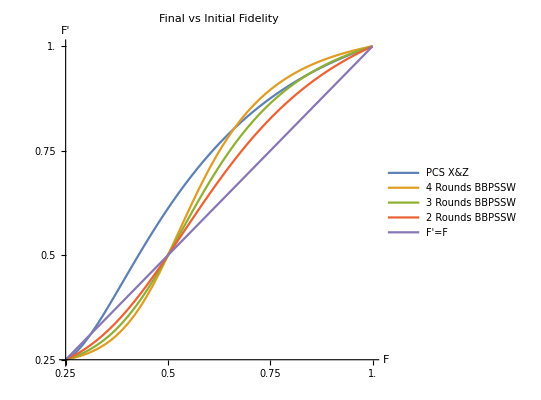

```mathematica
Plot[{fidpcs[F],bbpFid[ bbpFid[bbpFid[bbpFid[F]]]], bbpFid[bbpFid[bbpFid[F]]], bbpFid[bbpFid[F]], F},{F,1/4,1},  PlotLegends->Placed[{"PCS X&Z","4 Rounds BBPSSW","3 Rounds BBPSSW",  "2 Rounds BBPSSW", "F'=F"},{.8, .4}], AxesLabel->{"F", "F'"}, AspectRatio->1, PlotLabel->"Final vs Initial Fidelity", Ticks->{Range[1/4,1,0.25],Range[1/4,1,0.25]}]
```

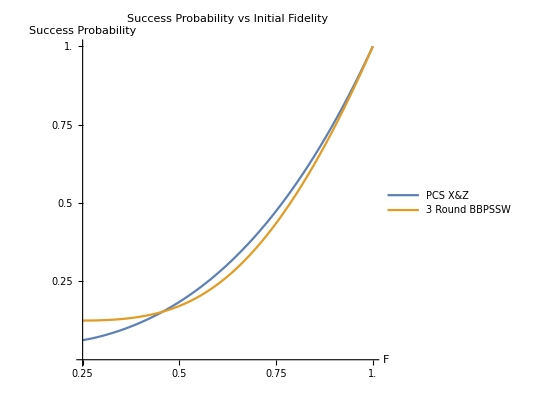

```mathematica
pcsPostselectFunc[F_]:=1/324 (3+6 F-√(-3+12 F)+4 F √(-3+12 F))^2
bbpSuccesFunc[F_]:=F^2+2F(1-F)/3+5((1-F)/3)^2
Plot[{pcsPostselectFunc[F],  bbpSuccesFunc[bbpFid[bbpFid[F]]] bbpSuccesFunc[bbpFid[F]]bbpSuccesFunc[F]},{F,1/4,1},  PlotLegends->Placed[{"PCS X&Z", "3 Round BBPSSW"},{.76, .25}], AxesLabel->{"F", "Success Probability"}, AspectRatio->1, PlotLabel->"Success Probability vs Initial Fidelity", PlotRange->{{1/4,1},{0,1}}, Ticks->{Range[1/4,1,0.25],Range[1/4,1,0.25]}]
```